```mathematica
f1[b_,alpha_,a_]:=NIntegrate[Sin[alpha+a*Sin[t]]/Sqrt[1+b^2*(1-Cos[alpha+a*Sin[t]])],{t,0.0,2*Pi}];
f2[b_,alpha_,a_]:=NIntegrate[Sin[alpha+a*Sin[t]]/Sqrt[0.0000001+b^2*(1-Cos[alpha+a*Sin[t]])],{t,0.0,2*Pi}];
```

```mathematica
list1=Flatten[Table[{alpha,a,f1[3,alpha,a]},{alpha,0.001,Pi,0.1},{a,0.1,10,0.1}],1];//AbsoluteTiming
list2=Flatten[Table[{alpha,a,f2[3,alpha,a]},{alpha,0.001,Pi,0.1},{a,0.1,10,0.1}],1];//AbsoluteTiming
```

{18.0076,Null}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.15377}. NIntegrate obtained 0.0188472 and 0.000107602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.15377}. NIntegrate obtained 0.00476484 and 0.000527484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.15377}. NIntegrate obtained 0.00627109 and 0.000528187 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{22.6387,Null}

```mathematica
ListPlot3D[{list1,list2},AxesLabel->{Style["α",FontSize->18],Style["a",FontSize->18]}]
```

-Graphics3D-

```mathematica
ListPlot3D[MapThread[{#1[[1]],#1[[2]],#1[[3]]-#2[[3]]}&,{list1,list2}],AxesLabel->{Style["α",FontSize->18],Style["a",FontSize->18]},PlotRange->All]
```

-Graphics3D-

```mathematica
a=3.2;
list11=Table[{alpha,f1[3,alpha,a]},{alpha,-Pi,Pi,0.05}];//AbsoluteTiming//Quiet
list12=Table[{alpha,f2[3,alpha,a]},{alpha,-Pi,Pi,0.05}];//AbsoluteTiming//Quiet
```

{0.528593,Null}

{0.601333,Null}

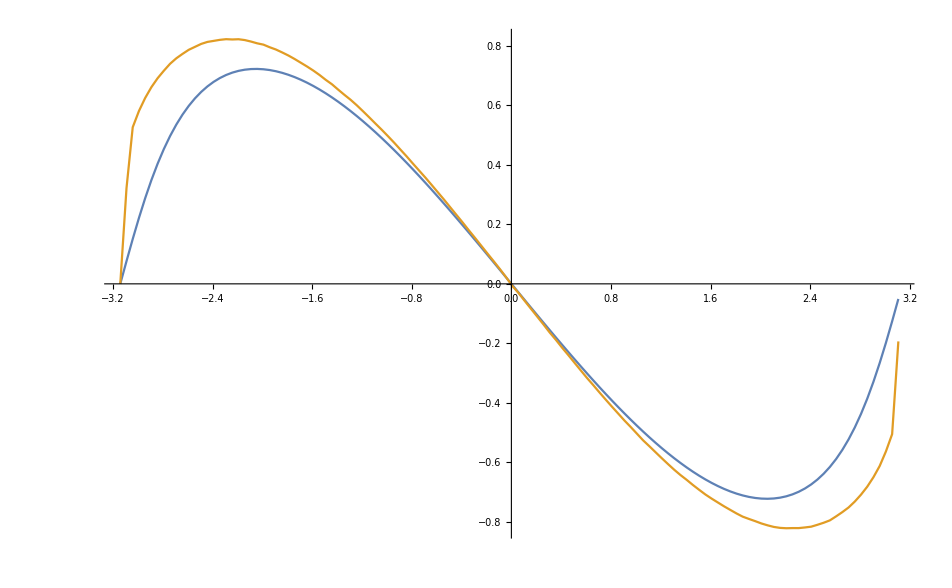

```mathematica
ListLinePlot[{list11,list12}]
```